Set up QuEST

```mathematica
SetDirectory[NotebookDirectory[]];

Import["https://qtechtheory.org/questlink.m"];
(*CreateLocalQuESTEnv[];*)
CreateDownloadedQuESTEnv[];
```

Function definitions

```mathematica
(* This little function is a way to generate a symbol like θ2
by using myθ[2] *)
(* IMPORTANT: We NEVER assign a value to a variable like θ2
it is always kept as a symbol. *)
(* The way we get a circuit with numerical values for gates,
is by REPLACING instances of the symbols with the values) *)
myθ[num_]:=ToExpression["θ"<>ToString[num]];

(* represents the circuit using the numerical parameters
stored in the global 'prms' variable *)
numericCirc[]:=encodeAnsatz/.Table[myθ[i]->prms[[i]],{i,numParams}];

ansatzCanDo:=
{"GHZ",
"Squeezed",
"GHZ tilted",
"Two GHZ states",
"All plus",
"All tilt",
"General product state",
"GeneralA",
"SpecialA",
"Custom"};

(* this function just creates an encoding ansatz circuit
of variety of kinds *)
CreateAnsatz[circuitN_,type_]:=Module[
{ansatz,ansatz1,ansatz2, paramCount,c,blocks,firstQs, qb,connectivity},
If[!MemberQ[ansatzCanDo,type],Beep[];Print["UNRECOGNISED CIRCUIT TYPE!"]];

If["GHZ"==type,
ansatz=Join[{Subscript[Ry, 0][π/2]}
,Table[Subscript[C, qb][Subscript[Ry, qb+1][π]],{qb,0,circuitN-2}]
,Table[Subscript[Rz, qb][θ1],{qb,0,circuitN-1}]];
paramCount=1;
];

If["Squeezed"==type,
(*This creates indexes of all possible
pairs of distinguished qubits*)
connectivity=Join[
Flatten[Table[{qb1,qb2},{qb1,0,circuitN-2},{qb2,qb1+1,circuitN-1}],1],
Flatten[Table[{qb2,qb1},{qb1,0,circuitN-2},{qb2,qb1+1,circuitN-1}],1]
];
ansatz=Join[
Table[Subscript[Ry, qb][π/2],{qb,0,circuitN-1}],
Table[Subscript[C, connectivity[[n,1]]][Subscript[Rz, connectivity[[n,2]]][θ1]],{n,1,Length@connectivity}],
Table[Subscript[Rx, qb][θ2],{qb,0,circuitN-1}],
Table[Subscript[Rz, qb][θ3],{qb,0,circuitN-1}]
];
paramCount=3;
];

If["GHZ tilted"==type,
ansatz=Join[{
Subscript[Ry, 0][θ1]}
,Table[Subscript[C, qb][Subscript[Ry, qb+1][π]],{qb,0,circuitN-2}]
,Table[Subscript[Rz, qb][θ2],{qb,0,circuitN-1}]
];
paramCount=2;
];

If["Two GHZ states"==type,
firstQs=Quotient[circuitN,2];
ansatz=Join[{Subscript[Ry, 0][π/2]}
,Table[Subscript[C, qb][Subscript[Ry, qb+1][π]],{qb,0,firstQs-2}]
,Table[Subscript[Rz, qb][θ1],{qb,0,firstQs-1}]];
ansatz=Join[ansatz,{Subscript[Ry, firstQs][π/2]}
,Table[Subscript[C, qb][Subscript[Ry, qb+1][π]],{qb,firstQs,circuitN-2}]
,Table[Subscript[Rz, qb][θ2],{qb,firstQs,circuitN-1}]];
paramCount=2;
];

If["All plus"==type,
ansatz=Join[
Table[Subscript[Ry, qb][π/2],{qb,0,circuitN-1}]
,Table[Subscript[Rz, qb][θ1],{qb,0,circuitN-1}]];
paramCount=1;
];

If["All tilt"==type,
ansatz=Join[Table[Subscript[Ry, qb][θ1],{qb,0,circuitN-1}]
,Table[Subscript[Rz, qb][θ2],{qb,0,circuitN-1}]
];
paramCount=2;
];

If["Independent tilt"==type,
ansatz={};
For[qb=0,qb<circuitN,qb++,
blocks=2*qb;
ansatz=Join[ansatz,{Subscript[Ry, qb][myθ[blocks+1]]
,Subscript[Rz, qb][myθ[blocks+2]]}];
];
paramCount=2*circuitN;
];

If["General product state"==type,
ansatz={};
For[qb=0,qb<circuitN,qb++,
blocks=3*qb;
ansatz=Join[ansatz,{Subscript[Rx, qb][myθ[blocks+1]]
,Subscript[Ry, qb][myθ[blocks+2]]
,Subscript[Rz, qb][myθ[blocks+3]]}
];
];
paramCount=3*circuitN;
];

If["SpecialA"==type,
ansatz={};
c=1;
For[blocks=1,blocks<=2,blocks++,
ansatz=Join[ansatz,Table[Subscript[Rx, qb][myθ[c++]],{qb,0,circuitN-1}]]; 
ansatz=Join[ansatz,Table[Subscript[C, qb][Subscript[Ry, Mod[qb+1,circuitN]][myθ[c++]]],{qb,0,circuitN-1,2}]];
ansatz=Join[ansatz,Table[Subscript[C, qb][Subscript[Ry, Mod[qb+1,circuitN]][myθ[c++]]],{qb,1,circuitN-1,2}]]; 
ansatz=Join[ansatz,Table[Subscript[Rz, qb][myθ[c++]],{qb,0,circuitN-1}]];
ansatz=Join[ansatz,Table[Subscript[C, Mod[qb+1,circuitN]][Subscript[Ry, qb][myθ[c++]]],{qb,0,circuitN-1,2}]];
ansatz=Join[ansatz,Table[Subscript[C, Mod[qb+1,circuitN]][Subscript[Ry, qb][myθ[c++]]],{qb,1,circuitN-1,2}]]; 

paramCount=c-1;
];
];

If["GeneralA"==type,
ansatz={};
c=1;
For[blocks=1,blocks<=2,blocks++,
ansatz=Join[ansatz,Table[Subscript[Rx, qb][myθ[c++]],{qb,0,circuitN-1}]];
 ansatz=Join[ansatz,Table[Subscript[C, qb][Subscript[Ry, Mod[qb+1,circuitN]][myθ[c++]]],{qb,0,circuitN-1,2}]];
ansatz=Join[ansatz,Table[Subscript[C, qb][Subscript[Ry, Mod[qb+1,circuitN]][myθ[c++]]],{qb,1,circuitN-1,2}]]; 
ansatz=Join[ansatz,Table[Subscript[Rz, qb][myθ[c++]],{qb,0,circuitN-1}]];
ansatz=Join[ansatz,Table[Subscript[C, Mod[qb+1,circuitN]][Subscript[Ry, qb][myθ[c++]]],{qb,0,circuitN-1,2}]];
ansatz=Join[ansatz,Table[Subscript[C, Mod[qb+1,circuitN]][Subscript[Ry, qb][myθ[c++]]],{qb,1,circuitN-1,2}]]; 
ansatz=Join[ansatz,Table[Subscript[Rz, qb][myθ[c++]],{qb,0,circuitN-1}]];
paramCount=c-1;
];
];

If["Custom"==type,
ansatz=Join[{Subscript[Ry, 0][π/2]}
,Table[Subscript[C, qb][Subscript[Ry, qb+1][π]],{qb,0,circuitN-2}]
,Table[Subscript[Rz, qb][θ1],{qb,0,circuitN-1}]];
paramCount=1;
];

Return@{ansatz,paramCount};
];

(* This function intialises quantum registers in QuEST *)
initStates[]:=Module[{},
{encodeAnsatz,numParams}=CreateAnsatz[numQs,thisAnsatzType];

DestroyAllQuregs[] ;

ψinitState = CreateQureg @ numQs; 
InitZeroState @ ψinitState;
(* this is a pure state, represented as a state vector. it will be set to |00...0> *)

ψinit = CreateDensityQureg @ numQs;
InitZeroState @ ψinit;
(* this is also a pure state, just the density matrix version of ψinitState *)

ϕ = CreateDensityQureg @ numQs;
Φ= CreateDensityQureg @ numQs;
Φtmp = CreateDensityQureg @ numQs;
(* these density matrices will store the working state of the circuit *)

(* The list 'prms' will store the actual paramter values, so θ1's value is prms[[1]] etc *)
(* we set the initial parameters to random values *)
prms=RandomReal[{0,4*Pi},numParams];

(* now we define the field strength, the noise type and the noise level *)
fieldStrength=0.1;
(* this is a small value equivalent to ΔB in the formalism *)

(* envTime is the time that the sensor state is exposed to the environment *)
(* envTime is a global variable, accessed directly by some functions *)
envTime=0.5;

envTimeMin=If["Indep. dephase on all qubits"==noiseType,0.02,0.06];

Return@0;
]

(* ========================================================= *)
(* Global variables are initialised to their default values by this function*)
(* Moreover, an interactive panel is set up for customising these global variables  *)
(* ========================================================= *)
initGlobalVariables[]:=Module[
{infoA,labelA,menuA,infoB,labelB,menuB,infoD,labelD,menuD},
infoA="specify the number of qubits";
numQs=4;
labelA="numQs = ";
menuA=PopupMenu[Dynamic[numQs],{1,2,3,4,5,6}];

infoB="Set up the ansatz type";
thisAnsatzType="GHZ";
labelB="thisAnsatzType = ";
menuB=PopupMenu[Dynamic[thisAnsatzType],ansatzCanDo];

infoD="Set up the noise type";
noiseType="Indep. dephase on all qubits";
labelD="noiseType = ";
menuD=PopupMenu[Dynamic[noiseType],noiseCanDo];

Print@Grid[{
{infoA,SpanFromLeft},{labelA,menuA},
{infoB,SpanFromLeft},{labelB,menuB},
{infoD,SpanFromLeft},{labelD,menuD}
},Alignment->{Left},
Background->{None,{{LightGray,None}}},
Spacings->{None,{0.4,0.4,2,0.4,2,0.4,2,0.4,2,0.4,2,0.4}}];

inited=False;
If[inited==False,
(* This adds the button *)
Print["\n\n",Button["re-initialize!",
initStates[];
initednoiseType=noiseType;
initedthisAnsatzType=thisAnsatzType;
initednumQs=numQs;
]
];
(* This initialises default parameters at first evaluation *)
initStates[];
inited=True;
initednoiseType=noiseType;
initedthisAnsatzType=thisAnsatzType;
initednumQs=numQs;
Print["The noise type will be '",Dynamic[initednoiseType],"'"];
Print["Now using the circuit '",Dynamic[initedthisAnsatzType],"' with ",
Dynamic[initednumQs]," qubits and therefore ",
Dynamic[numParams]," parameters:"];
Print[Dynamic[DrawCircuit[encodeAnsatz]]];
];

Return@0;]


noiseCanDo=
{"Depol. on Q0",
"Indep. depol. on all qubits",
"Indep. dephase on all qubits",
"Indep. amplitude damping all qubits",
"Indep. time correlated dephasing all qubits",
"Indep. inhom. Pauli all qubits",
"Custom Kraus map"
};

(* This function applies the enviroment, including the B field and the noise, to the qubits *)
(* An example of usage is applyEnvToϕ[0.5,"Indep. depol. on all qubits"] which means the *)
(* field strength is 0.5 *)

applyEnvToϕ[fieldStr_,type_]:=Module[
{field,qb,ms,i,j,denMat,denMat2,maxFieldQb,
effectiveLevel,noiseKrausOperators,combinedKrausOps,probx,proby,probz},

If[!MemberQ[noiseCanDo,type],Beep[];Print["UNRECOGNISED NOISE TYPE!"]];

maxFieldQb=numQs;

If["Depol. on Q0"==type, (* this noise type commutes with field *)
effectiveLevel=0.75*(1-Exp[-envTime]);
ApplyCircuit[{Subscript[Depol, 0][effectiveLevel]}, ϕ];
ApplyCircuit[field, ϕ ];
];

If["Indep. depol. on all qubits"==type,(* this noise type commutes with field *)
effectiveLevel=0.75*(1-Exp[-envTime]);
For[qb=0,qb<numQs,qb++,
ApplyOneQubitDepolariseError[ϕ,qb,effectiveLevel];
];
field=Table[Subscript[Rz, qb][fieldStr*envTime],{qb,0,maxFieldQb-1}];
ApplyCircuit[field, ϕ ];
];

If["Indep. dephase on all qubits"==type,(* this noise type commutes with field *)
effectiveLevel=0.5*(1-Exp[-envTime]);

For[qb=0,qb<numQs,qb++,
ApplyOneQubitDephaseError[ϕ,qb,effectiveLevel];
];
field=Table[Subscript[Rz, qb][fieldStr*envTime],{qb,0,maxFieldQb-1}];
ApplyCircuit[field, ϕ ];
];

If["Indep. amplitude damping all qubits"==type,
(* this noise type commutes with field *)
effectiveLevel=1.0*(1-Exp[-envTime]);
For[qb=0,qb<numQs,qb++,
ApplyOneQubitDampingError[ϕ,qb,effectiveLevel];
];
field=Table[Subscript[Rz, qb][fieldStr*envTime],{qb,0,maxFieldQb-1}];
ApplyCircuit[field, ϕ ];
];

If["Indep. time correlated dephasing all qubits"==type,
(* this noise type commutes with field *)
effectiveLevel=0.5*(1-Exp[-envTime^2]);

For[qb=0,qb<numQs,qb++,
ApplyOneQubitDephaseError[ϕ,qb,effectiveLevel];
];
field=Table[Subscript[Rz, qb][fieldStr*envTime],{qb,0,maxFieldQb-1}];
ApplyCircuit[field, ϕ ];
];


If["Indep. inhom. Pauli all qubits"==type,
effectiveLevel=0.75*(1-Exp[-1]);
(* This is now a Pauli error -- its parameters are scaled to the previous error types *)
(* i.e., the Kraus map is defined which corresponds to severity*envTime=1 *)
{probx,proby,probz}={0.1,0.2,0.05};
{probx,proby,probz}={probx,proby,probz}/(probx+proby+probz)*effectiveLevel;
noiseKrausOperators=pauliKraussOperators[probx,proby,probz];
(* This error channel is combined with the free-field evolution into one Kraus map *)
combinedKrausOps=fieldWithNoiseKraus[fieldStr,noiseKrausOperators,envTime];

field=Table[Subscript[Kraus, qb][combinedKrausOps],{qb,0,maxFieldQb-1}];
ApplyCircuit[field, ϕ ];
];

If["Custom Kraus map"==type,
(* An arbitrary noise channel can be specified here via its Kraus operators *)
noiseKrausOperators=customKrausOperators;
(* This error channel is combined with the free-field evolution into one Kraus map *)
combinedKrausOps=fieldWithNoiseKraus[fieldStr,noiseKrausOperators,envTime];

field=Table[Subscript[Kraus, qb][combinedKrausOps],{qb,0,maxFieldQb-1}];
ApplyCircuit[field, ϕ ];
];

];
(* ========================================================= *)
(* Below are Kraus operators of typical error models *)
(* ========================================================= *)
dephaseKraussOperators[p_]:={Sqrt[(1-p)]*PauliMatrix[0],Sqrt[p]*PauliMatrix[3]};
depolariseKraussOperators[p_]:={Sqrt[(1-p)]*PauliMatrix[0],Sqrt[p/3]*PauliMatrix[1],Sqrt[p/3]*PauliMatrix[2],Sqrt[p/3]*PauliMatrix[3]};
pauliKraussOperators[px_,py_,pz_]:={Sqrt[(1-px-py-pz)]*PauliMatrix[0],Sqrt[px]*PauliMatrix[1],Sqrt[py]*PauliMatrix[2],Sqrt[pz]*PauliMatrix[3]};
amplitudeDampingKraussOperators[gamma_]:={
{{1,0},{0,Sqrt[1-gamma]}},
{{0,Sqrt[gamma]},{0,0}}
}

(* ========================================================= *)
(* Below are functions used for manipulating Kraus maps *)
(* ========================================================= *)
quantumChannelSuperOperator[kraussOperators_]:=
Sum[
KroneckerProduct[Conjugate@kraussOperators[[n]],kraussOperators[[n]]]
,{n,1,Length@kraussOperators}]

superOperator2KrausMap[supOp_]:=Module[{pauliBases,pauliDecomposition,check,norm,result,eigvals,eigvecs},
pauliBases=Table[
KroneckerProduct[Conjugate@PauliMatrix[m],PauliMatrix[n]]
,{m,0,3},{n,0,3}];
pauliDecomposition=Table[
Tr[ConjugateTranspose[pauliBases[[m+1,n+1]]].supOp]/4
,{m,0,3},{n,0,3}];
{eigvals,eigvecs}=Eigensystem@pauliDecomposition;

result=Table[
Sqrt[eigvals[[n]]]*Sum[
PauliMatrix[m-1]*(ConjugateTranspose@eigvecs)[[m,n]]
,{m,1,4}],
{n,1,4}];

check=quantumChannelSuperOperator[result];
norm=Sqrt@Total[Abs[check-supOp]^2,2];
If[norm>10^(-10),Print["ERROR!!!  non-zero difference when transforming superoperator to Kraus map: ",norm]
];
Return@result;
]


fieldWithNoiseKraus[fieldStrength_,noiseKrausOperators_,  time_]:=Module[{Rotz,freeNoiseSupOp,freeFieldSupOp,noiseGen,freeFieldGen,combKrausOps},
Rotz[α_]:=Cos[α/2]*PauliMatrix[0]-I*Sin[α/2]*PauliMatrix[3];
freeNoiseSupOp=quantumChannelSuperOperator@noiseKrausOperators;
freeFieldSupOp=quantumChannelSuperOperator[{Rotz[fieldStrength]}];
noiseGen=MatrixLog@freeNoiseSupOp;
freeFieldGen=MatrixLog@freeFieldSupOp;
combKrausOps=superOperator2KrausMap@MatrixExp[(freeFieldGen+noiseGen)*time];
Return[Chop@combKrausOps];
]


CombineKrausMaps[Kraus1_,Kraus2_]:=Module[{SupOp1,SupOp2},
SupOp1=quantumChannelSuperOperator[Kraus1];
SupOp2=quantumChannelSuperOperator[Kraus2];
Return@Chop@superOperator2KrausMap[
MatrixExp[MatrixLog@SupOp1+MatrixLog@SupOp2]
];
]

(* this calculates the fidelity between two denity matrices *)
fidelity[rho1_,rho2_]:=Module[{sq,sq2,result,localrho1,localrho2},
localrho1=(rho1+ConjugateTranspose@rho1)/2;
localrho2=(rho2+ConjugateTranspose@rho2)/2;
sq=MatrixPower[localrho1,1/2];
sq2=sq.Chop[localrho2].sq;
result=Abs@Tr@MatrixPower[sq2,1/2]^2;
If[result>1.,Return@1.,If[result<0,Return@0.,Return@result]];
]
(* This function works out how good a proposed circuit (WITHOUT decode) is at sensing *)
(* in princple. The usage is e.g. CalcFigureOfMerit[circ,0.5,"Indep. depol. on all qubits",0.1] where *)
(* field=0.5, noise=0.1, noise type is Indep. depol., and circ is the trial circuit *)

CalcFigureOfMerit[numericCirc_,noiseType_]:=Module[{rho1, rho2, tmp},

ApplyCircuit[numericCirc, ψinit, ϕ ];
(*Cloning to store circ output...."*)
CloneQureg[Φ,(* <== *)ϕ];

(* First model the case with B=0 *)
applyEnvToϕ[0.,noiseType];

(* Cloning to store env1 output and restore circ to ϕ *)
CloneQureg[Φtmp,(* <== *)ϕ];
CloneQureg[ϕ,(* <== *)Φ];

(* Now model the case with B=δB *)
applyEnvToϕ[fieldStrength,noiseType];

rho1=GetQuregMatrix[Φtmp];
rho2=GetQuregMatrix[ϕ];

If[envTime<envTimeMin,Beep[];Print["too short envTime!"]];
tmp=4*(1-fidelity[rho1,rho2])/fieldStrength^2/envTime;

Return@If[! MachineNumberQ[tmp], 0., tmp];

]
localMaximise[]:=Module[{},
costF[vars_]:=Module[{},
step++;
Do[
If[MachineNumberQ@vars[[i]]
,prms[[i]]=vars[[i]],prms[[i]]=0.];
,{i,numParams}];
If[(MachineNumberQ@vars[[numParams+1]]),envTime=vars[[numParams+1]],envTime=0.5];
If[envTime>envTimeMin,
Return@CalcFigureOfMerit[numericCirc[],noiseType];
,Return[-Abs@envTime];
];
];

stepString[actualValue_,step_]:=
StringJoin["Optmisation running....\n";"Number of Qubits: ", ToString@numQs,"  noise: ", noiseType ,"\nnumber of opt.: ",ToString@try,
"\non step: ", ToString@step, "  F= ", ToString@actualValue, "  prms= ", ToString@vars];

doMathematicaOptimise[]:=FindMaximum[
If[vars==null||vars!=null,actualValue=costF[vars]]
,varsInit
,AccuracyGoal->3,PrecisionGoal->3
,Method->"PrincipalAxis"
,EvaluationMonitor:>(mon=stepString[actualValue,step])
];

If["All plus"==thisAnsatzType,
envTimeGuess=1;
,If["GHZ"==thisAnsatzType
,envTimeGuess=1/(numQs);
,envTimeGuess=1/(Sqrt[numQs]);
];
];

var[num_]:=ToExpression["var"<>ToString[num]];
vars=Table[var[i],{i,numParams+1}];
varsInit=Table[{var[i],
If[i==numParams+1,envTimeGuess,RandomReal[{-π,π}]]
},{i,numParams+1}];

null=Table[0,{i,numParams+1}];
step=0;
Monitor[result=doMathematicaOptimise[];,mon];

Return@result;
]
reportOptimization[]:=Print[
"================RESULTS==========================================="
,"\n Number of Qubits: ", numQs
,"\n Circuit '",thisAnsatzType,"'"
,"\n noise type '",noiseType,"'"
,"\n envTime=",envTime
,"\n On step=",step
,"\n Precision  = ",theMerit
,"\n==========================================================="
];
optimiseParameters[numOptimisations_]:=(
dataset={};
Do[
initStates[];
result=localMaximise[];
theMerit=result[[1]];
prms=vars/.result[[2]];
envTime=prms[[numParams+1]];
prms=prms[[1;;numParams]];

dataset=Join[dataset,{{numQs,theMerit,envTime,prms}}];
,{try,1,numOptimisations}];

maxpos=Position[dataset,Max@dataset[[All,2]]][[1,1]];
{numQs,theMerit,envTime,prms}=dataset[[maxpos]];
reportOptimization[];
)
plotFCT[data_]:=Grid[{{
Show[
ListPlot[data[[All,1;;2]],PlotStyle->Directive[Red,PointSize[Large]]],
ListLinePlot[data[[All,1;;2]],PlotStyle->Directive[Thick, Black]]
,PlotRange->{{1,maxNumQs*1.2},All}
,AxesOrigin->{1,0}
,TicksStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->Medium]
,LabelStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->Medium],
ImageSize->Medium,
AxesLabel->{"numQs","Precision"}
]
,
Show[
ListPlot[data[[All,1;;3;;2]],PlotStyle->Directive[Red,PointSize[Large]]],
ListLinePlot[data[[All,1;;3;;2]],PlotStyle->Directive[Thick, Black]]
,PlotRange->{{1,maxNumQs*1.2},All}
,AxesOrigin->{1,0}
,TicksStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->Medium]
,LabelStyle->Directive[Black,FontFamily->"Times New Roman",FontSize->Medium],
ImageSize->Medium,
AxesLabel->{"numQs","envTime"}
]
}}]
```

Initialise quantum registers

```mathematica
initGlobalVariables[];
```

specify the number of qubits | 
numQs =  | 
Set up the ansatz type | 
thisAnsatzType =  | 
Set up the noise type | 
noiseType =  |

re-initialize!

The noise type will be ''

Now using the circuit '' with  qubits and therefore  parameters:

Run the  optimisation for the preselected noise model and circuit type

Abort computation

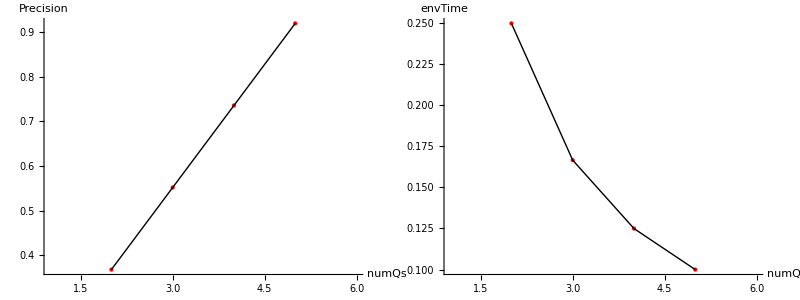

```mathematica
(* The metrological precision is calculated up to 'maxNumQs' qubits *)
maxNumQs=5;
(* The optimisation is repeated this many times to ensure the global maximum is found *)
numberOfLocalOptimisations=5;


graphdata=ConstantArray[0.,{maxNumQs-1,3}];
break=False;
(* Do the optimisation and plot the figure in real time *)
Monitor[
Print@Button["Abort computation",Dynamic[break=True]];
Do[
Do[
If[break==True,Abort[]];
initStates[];
result=localMaximise[];
theMerit=result[[1]];
ps=vars/.result[[2]];
envTime=ps[[numParams+1]];
If[theMerit>graphdata[[numQs-1,2]],graphdata[[numQs-1]]={numQs,theMerit,envTime}];
,{try,1,numberOfLocalOptimisations}];
,{numQs,2,maxNumQs}];
,plotFCT[DeleteCases[graphdata,{0.,0.,0.}]]
]

plotFCT[DeleteCases[graphdata,{0.,0.,0.}]]
```

More details on how the program works

Indep. dephase on all qubits

4

GHZ

{Ry_0[π/2],C_0[Ry_1[π]],C_1[Ry_2[π]],C_2[Ry_3[π]],C_3[Ry_4[π]],Rz_0[θ1],Rz_1[θ1],Rz_2[θ1],Rz_3[θ1],Rz_4[θ1]}

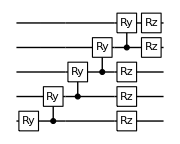

```mathematica
(* These global variables were initialised previously and their
current values are:*)

(* This is the noise model used in the simulations *)
noiseType

(* number of qubits *)
numQs

(* Type of probe state to be optimised *)
thisAnsatzType

(* Circuit representation of the probe state that will be used in QuEST *)
encodeAnsatz
DrawCircuit[encodeAnsatz]
```

{Ry_0[π/2],C_0[Ry_1[π]],C_1[Ry_2[π]],C_2[Ry_3[π]],Rz_0[θ1],Rz_1[θ1],Rz_2[θ1],Rz_3[θ1]}

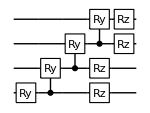

```mathematica
(* The variable 'encodeAnsatz' can be customised manually 
-- the customised circuit will be then used in the calculations
*)

(* This is an example circuit *)
customAnsatz=Join[{Subscript[Ry, 0][π/2]}
,Table[Subscript[C, qb][Subscript[Ry, qb+1][π]],{qb,0,numQs-2}]
,Table[Subscript[Rz, qb][θ1],{qb,0,numQs-1}]]
DrawCircuit[customAnsatz]
(* the number of free parameters must also be set*)
customnumParams=1;

(* if the 'Custom' circuit option is selected from the menu then this ansatz
will be used in the optimisations *)
If[thisAnsatzType=="Custom",{encodeAnsatz,numParams}={customAnsatz,customnumParams};];
(* info is now automatically updated below the dropdown menu *)
```

```mathematica
(* Arbitrary noise models can be used by defining
 Kraus operators of the process*)
(* Specify the Kraus map that occurs at
time t=1 (in units of the decay time) *)
prob=0.5(1-Exp[-1])
(* The example here is a bitflip error *)
customKrausOperators={Sqrt[1-prob]*PauliMatrix[0],Sqrt[prob]*PauliMatrix[1]}
(* This noise type will be used in the calculations if the 'Custom Kraus map' option is selected in the dropdown menu *)
```

0.31606

{{{0.827006,0.},{0.,0.827006}},{{0.,0.562192},{0.562192,0.}}}

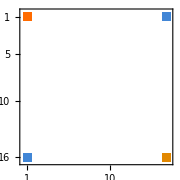

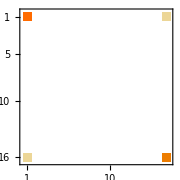

```mathematica
(* initialise random circuit parameters for 5 qubits*)
numQs=4;
initStates[];
prms=RandomReal[{-2*Pi,2*Pi},numParams];
(* apply the preset ansatz circuit to the
reference state 'ψinit' and store the result in 'ϕ'*)
ApplyCircuit[numericCirc[], ψinit, ϕ ];
(* This now plots the resulting density matrix *)
MatrixPlot[Chop@GetQuregMatrix[ϕ],ImageSize->Small]


(*Now apply noise and externa field evolution to the initialised state *)
applyEnvToϕ[fieldStrength,noiseType]
(* This changes the density matrix *)
MatrixPlot[Chop@Abs@GetQuregMatrix[ϕ],ImageSize->Small]
```

```mathematica
(* initialise random circuit parameters for 5 qubits*)
numQs=4;
initStates[];
prms=RandomReal[{-2*Pi,2*Pi},numParams];

(* Caclulate the dimensionless precision -- this function will be used as the figure of merit for the optimisations *)
CalcFigureOfMerit[numericCirc[],noiseType]
```

0.146037

```mathematica
(* Optmisie parameters of the circuit *)
numQs=4;
initStates[];
numberOfLocalOptimisations=5;
optimiseParameters[numberOfLocalOptimisations]
```

================RESULTS===========================================
 Number of Qubits: 4
 Circuit 'GHZ'
 noise type 'Indep. dephase on all qubits'
 envTime=0.124948
 On step=59
 Precision  = 0.735606
===========================================================